## 多线程运行

注： 命令行输入 top 查看 CPU 占用情况

### 测试阶段

#### 函数-Parallelize

并行运算，自动化进行

```mathematica
f1[n_]:=Length[FactorInteger[(10^n-1)/9]];
f1/@Range[70]//Last//Timing
```

{4.54149,12}

```mathematica
Parallelize[Map[f1,Range[70]]]//Last//Timing
```

{0.185287,12}

```mathematica
$KernelCount
```

4

#### 函数-ParallelTry

并行运算，其中一个得到结果时停止

```mathematica
ClearAll[f];
f[x_]:=(Pause[RandomInteger[{1,100}]/20];
Print[x,"\t",$KernelCount];
Pause[RandomInteger[{20}]];
Print[x+10,"\t",$KernelCount];
x+20);
```

```mathematica
ParallelTry[f,Range@10]
```

1	4

2	4

3	4

4	4

14	4

24

#### 内核

```mathematica
$KernelCount
```

```mathematica
(*新增内核*)
LaunchKernels[10];
```

```mathematica
(*关闭内核*)
CloseKernels[];
```

#### 函数-ParallelMap

```mathematica
LaunchKernels[10];
```

```mathematica
ParallelMap[f,Range@20]
```

#### 临界区（全局解释器锁）

相关函数

```mathematica
SetSharedVariable
DistributeDefinitions
CriticalSection
```

```mathematica
(*没有设置锁*)
SetSharedVariable[xs];
xs=0;
ParallelDo[xs=xs+1,{10}];
xs
```

4

```mathematica
(*设置锁*)
SetSharedVariable[xs];
xs=0;
ParallelDo[CriticalSection[a,xs=xs+1],{10}];
xs
```

10

#### 测试全局锁

```mathematica
CloseKernels[];
LaunchKernels[5];
```

单个锁

```mathematica
ClearAll[f,lock];
SetSharedVariable[var];
var=0;
f[x_]:=(Pause[RandomInteger[{1,100}]/20];
Print[x,"\t",$KernelCount];
Pause[RandomInteger[{20}]/20];
Print[x+10,"\t",$KernelCount];
CriticalSection[lock,Print["here I lock something\t",var=var+1];];
x+20);
ParallelMap[f,Range@8]
```

两个锁

```mathematica
ClearAll[f,lock1,lock2];
f[n_]:=If[n==1||n==4,CriticalSection[lock1,Print["lock 1\t",n];Pause[5]],CriticalSection[lock2,Print["lock 2\t",n];Pause[1]]];
```

```mathematica
ParallelMap[f,Range@8]
```

lock 1	1

lock 2	3

lock 2	5

lock 2	6

lock 2	7

lock 2	8

lock 1	4

lock 2	2

{Null,Null,Null,Null,Null,Null,Null,Null}

### 准备函数

#### 内容汇总

——基础函数——
GraphF[k_?Positive]
	构造特殊子图 F_k
GraphK3[k_?Positive]
	K3 的若干 copies
SubGraph
	判别是否为子图
ExtremalGraphs[graphs_,forbidden_,edge_:0]
	从给定图中筛选子图

——简单图相关数据——
第八阶 12 346
第九阶 274 668
第十阶 12 005 168
第十一阶 1 018 997 864

——文件分割——
第九阶 8
第十阶 391
第十一阶 -

#### 导入函数

```mathematica
SetDirectory[NotebookDirectory[]]
<<extremal.m;
?Extremal`*
```

/home/rex/desktop/work_space/1 MMA/4 ExtremalGraphs

Loading functions about extremal graphs...

#### 获取部分简单图

```mathematica
SimpleGraphs[n_,a_,b_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph"<>ToString@n<>".g6",{"GraphList",Range[a,b]}];
```

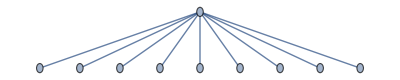
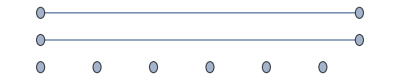
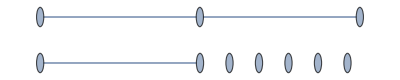
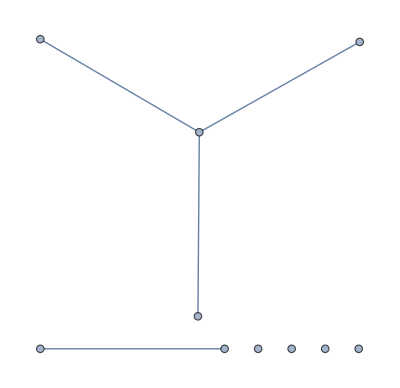
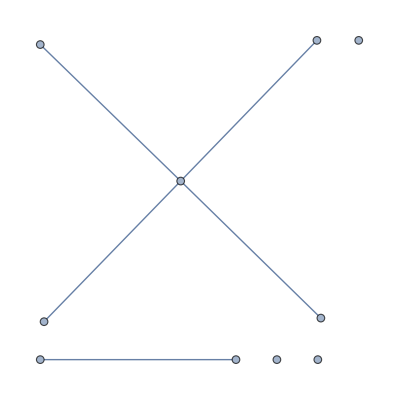
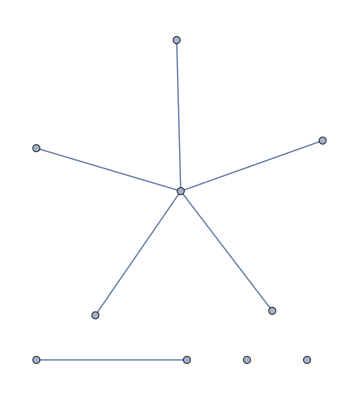

```mathematica
SimpleGraphs[10,10,15]
```

```mathematica
path="~/desktop/work_space/1 MMA/0 pkg/simplegraphs";
SimpleGraphs[n_,k_]:=Import[ToString@StringForm["`1`/graph`2`/graph`2`-`3`.g6",path,n,k]];
```

```mathematica
graphs=SimpleGraphs[9,1];
```

#### 多线程拆分

```mathematica
SetDirectory[NotebookDirectory[]];
ParallelNeeds["Extremal`"];
```

```mathematica
LaunchKernels[50];
$KernelCount
```

150

```mathematica
ClearAll[lock];
SetSharedVariable[size,step,n,medge,graphs,forbidden];
Needs["Extremal`"]
(*size of simple graphs of n vertices*)
forbidden=GraphF[2];
{n,size}={9,274668};
(*{n,size}={8,12346};*)
step=10^3;
(*output results*)
medge=0;
graphs={};
```

```mathematica
ChkPart[k_]:=Module[{edge=medge,newgraphs,a,b},
{a,b}={(k-1) step+1,k step};
If[a>size,Return[Nothing]];
If[b>size,b=size];
{newgraphs,edge}=ExtremalGraphs[SimpleGraphs[n,a,b],forbidden,edge];
CriticalSection[lock,Which[
edge<medge,Return[Nothing],
edge>medge,medge=edge;graphs=newgraphs,
edge==medge,medge=edge;graphs=Join[graphs,newgraphs]]];Nothing]
```

### 调试使用

#### 公共内容

```mathematica
SetDirectory[NotebookDirectory[]];
ParallelNeeds["Extremal`"];
Needs["Extremal`"]
```

Loading functions about extremal graphs...

```mathematica
ClearAll[lock];
SetSharedVariable[size,medge,graphs,forbidden,tmp,checked];
tmp=FileNameJoin[{NotebookDirectory[],"saved.wl"}];
forbidden=GraphF[3];
checked={};
```

```mathematica
ChkPart[n_][k_]:=ChkPart[n,k];
ChkPart[n_,k_]:=Module[{edge,newgraphs},
If[MemberQ[checked,k],Return@Nothing];
{newgraphs,edge}=ExtremalGraphs[SimpleGraphs[n,k],forbidden,medge];
CriticalSection[lock,
If[edge>medge,medge=edge;graphs=newgraphs,
If[edge==medge,graphs=Join[graphs,newgraphs]]];
(*Print[k,"\tmedge:",medge,"\textremal graphs:",Length@graphs];*)
AppendTo[checked,k](*Save[tmp,checked];*)
];
Nothing]
```

#### 第九阶

```mathematica
{n,size}={9,8};
CloseKernels[];
LaunchKernels[7];
$KernelCount
```

```mathematica
medge=0;graphs={};
ParallelMap[ChkPart[n],Range@size]//Timing
```

Checked:	9	8
newgraphs:0	medge:0	extremal graphs:0

Checked:	9	1
newgraphs:1	medge:21	extremal graphs:1

Checked:	9	5
newgraphs:1	medge:21	extremal graphs:2

Checked:	9	3
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	6
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	4
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	7
newgraphs:0	medge:21	extremal graphs:2

Checked:	9	2
newgraphs:0	medge:21	extremal graphs:2

{1.68937,{}}

#### 第十阶

51 线程用时 488s
101 线程用时 278 - 290s

```mathematica
{n,size}={10,391};
(*CloseKernels[];*)
AbsoluteTiming[LaunchKernels[50];]
$KernelCount
```

{32.8167,Null}

50

### 计算数据

```mathematica
forbidden=GraphF[4]
```

-Graphics-

#### part 1

{20.7595,{}}

30

{5,7,8,1,6,9,2,3,4}

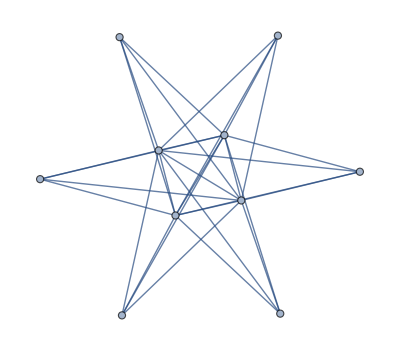

```mathematica
medge=0;graphs={};
Monitor[ParallelMap[ChkPart[n],Range[Min[9,size]]]//Timing,{medge,Length@checked,"\n",graphs}]
medge
graphs
```

{137.685,{}}

32

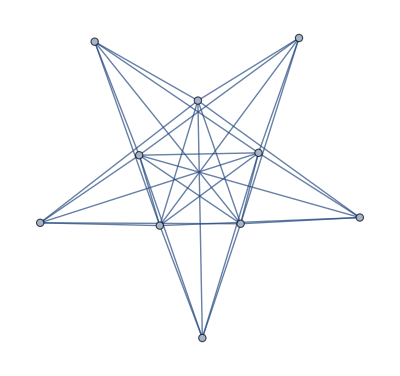

```mathematica
Monitor[ParallelMap[ChkPart[n],Range[10,100]]//Timing,{medge,Length@checked,"\n",graphs}]
medge
graphs
```

#### Part 2

```mathematica
checked=Range@100;
```

```mathematica
Monitor[ParallelMap[ChkPart[n],Range[101,200]]//Timing,{medge,Length@checked,"\n",graphs}]
checked
graphs
```

{135.663,{}}

{5,7,8,1,6,9,2,3,4,97,54,36,90,46,94,48,99,24,32,26,93,98,64,82,95,92,10,42,44,66,74,86,52,68,96,84,16,22,34,72,14,18,40,62,76,20,30,50,28,56,58,60,70,78,80,88,12,100,38,89,91,65,25,27,55,87,67,83,49,45,11,37,47,31,43,33,19,41,75,23,71,85,53,59,63,29,69,51,77,21,61,13,73,79,81,15,17,35,39,57,155,121,189,195,153,185,135,143,125,161,111,197,117,139,157,131,167,119,123,147,193,159,109,115,129,137,145,179,169,173,175,165,181,199,101,103,105,107,163,177,183,187,113,133,141,149,151,171,191,127,156,190,122,112,116,118,144,110,140,158,162,132,196,136,180,126,154,138,176,186,124,168,120,194,198,160,166,184,192,170,182,148,106,108,200,102,130,164,172,188,128,104,152,174,178,142,114,134,146,150}

{-Graphics-}

#### Part 3

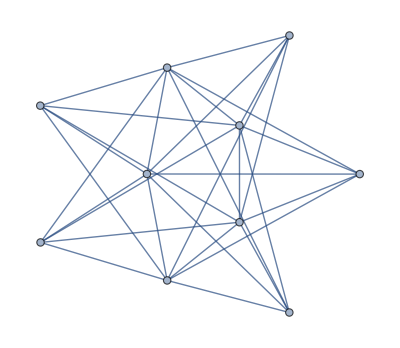
```mathematica
checked=Range@200;
(*medge=30;
graphs={-Graphics-};*)
```

{113.49,{}}

{5,7,8,1,6,9,2,3,4,97,54,36,90,46,94,48,99,24,32,26,93,98,64,82,95,92,10,42,44,66,74,86,52,68,96,84,16,22,34,72,14,18,40,62,76,20,30,50,28,56,58,60,70,78,80,88,12,100,38,89,91,65,25,27,55,87,67,83,49,45,11,37,47,31,43,33,19,41,75,23,71,85,53,59,63,29,69,51,77,21,61,13,73,79,81,15,17,35,39,57,155,121,189,195,153,185,135,143,125,161,111,197,117,139,157,131,167,119,123,147,193,159,109,115,129,137,145,179,169,173,175,165,181,199,101,103,105,107,163,177,183,187,113,133,141,149,151,171,191,127,156,190,122,112,116,118,144,110,140,158,162,132,196,136,180,126,154,138,176,186,124,168,120,194,198,160,166,184,192,170,182,148,106,108,200,102,130,164,172,188,128,104,152,174,178,142,114,134,146,150,247,261,243,249,221,227,215,231,273,285,201,229,253,299,275,235,281,245,257,269,237,271,295,277,267,289,207,219,239,241,263,203,223,225,265,293,217,279,291,233,251,211,213,259,255,287,297,209,283,205,222,232,248,216,276,228,274,292,262,244,254,250,226,230,286,266,258,290,300,278,202,282,298,218,264,224,236,246,242,294,296,260,220,208,270,272,212,234,288,210,240,256,268,204,206,252,238,280,284,214}

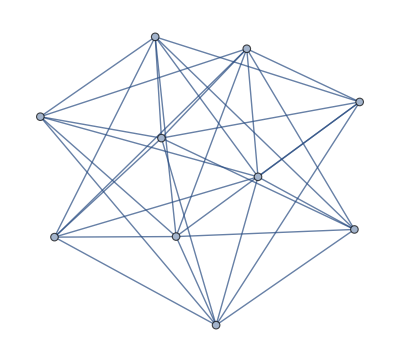
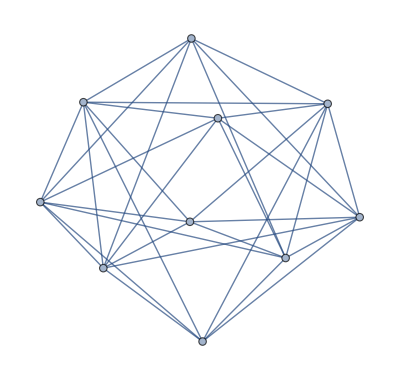

```mathematica
Monitor[ParallelMap[ChkPart[n],Range[201,300]]//Timing,{medge,Length@checked,"\n",graphs}]
checked
graphs
```

{142.881,{}}

{5,7,8,1,6,9,2,3,4,97,54,36,90,46,94,48,99,24,32,26,93,98,64,82,95,92,10,42,44,66,74,86,52,68,96,84,16,22,34,72,14,18,40,62,76,20,30,50,28,56,58,60,70,78,80,88,12,100,38,89,91,65,25,27,55,87,67,83,49,45,11,37,47,31,43,33,19,41,75,23,71,85,53,59,63,29,69,51,77,21,61,13,73,79,81,15,17,35,39,57,155,121,189,195,153,185,135,143,125,161,111,197,117,139,157,131,167,119,123,147,193,159,109,115,129,137,145,179,169,173,175,165,181,199,101,103,105,107,163,177,183,187,113,133,141,149,151,171,191,127,156,190,122,112,116,118,144,110,140,158,162,132,196,136,180,126,154,138,176,186,124,168,120,194,198,160,166,184,192,170,182,148,106,108,200,102,130,164,172,188,128,104,152,174,178,142,114,134,146,150,247,261,243,249,221,227,215,231,273,285,201,229,253,299,275,235,281,245,257,269,237,271,295,277,267,289,207,219,239,241,263,203,223,225,265,293,217,279,291,233,251,211,213,259,255,287,297,209,283,205,222,232,248,216,276,228,274,292,262,244,254,250,226,230,286,266,258,290,300,278,202,282,298,218,264,224,236,246,242,294,296,260,220,208,270,272,212,234,288,210,240,256,268,204,206,252,238,280,284,214,391,319,301,347,373,369,353,379,349,384,315,331,333,337,345,361,371,377,385,386,387,388,317,323,335,339,341,343,351,355,357,390,303,305,307,309,311,313,321,325,327,329,359,363,365,367,375,381,383,389,302,320,370,374,316,348,350,354,332,380,338,346,318,378,362,334,372,340,344,324,336,306,310,352,356,358,312,314,322,328,330,342,382,304,364,366,308,326,360,368,376}

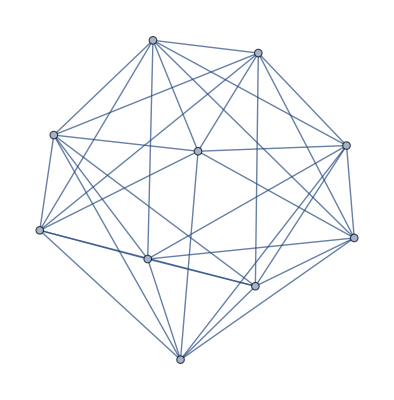
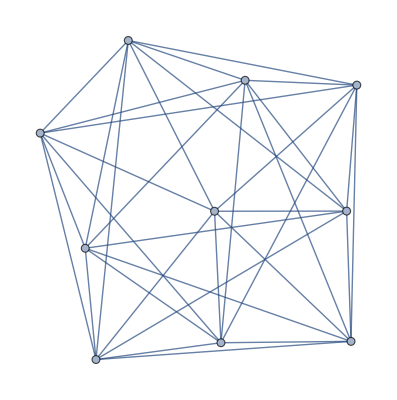
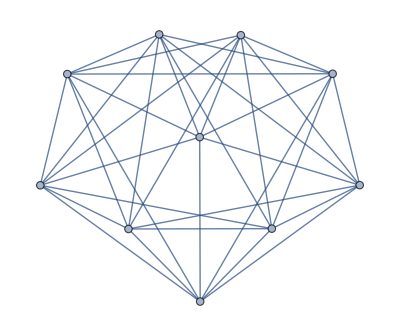
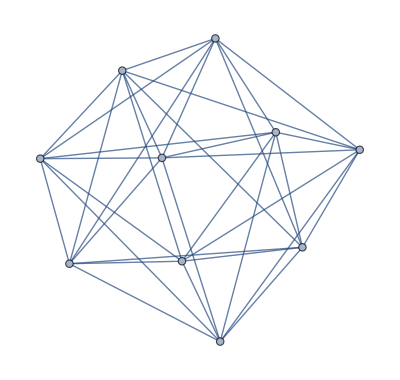
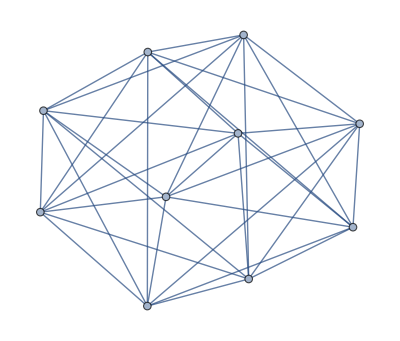

```mathematica
Monitor[ParallelMap[ChkPart[n],Range[301,size]]//Timing,{medge,Length@checked,"\n",graphs}]
checked
graphs
```

```mathematica
medge
```

35

#### graph

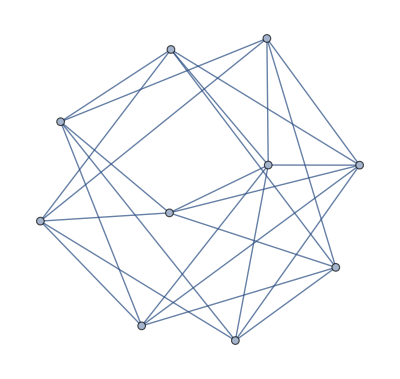

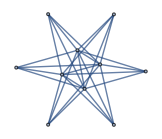

#### IO 编程

```mathematica
tmp=FileNameJoin[{NotebookDirectory[],"saved.wl"}];
a={1,2};
b=2;
Save[tmp,{a,b}]
```

```mathematica
Clear[a,b]
```

```mathematica
Get[tmp]
```

2

```mathematica
DeleteFile[tmp]
```